```mathematica
Import[FileNameJoin[{NotebookDirectory[],"modules/breed.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/fitfunctions.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"modules/generators.m"}]];
Import [FileNameJoin[{NotebookDirectory[],"modules/phenotypes.m"}]];
```

```mathematica
img1Data = Import[FileNameJoin[{NotebookDirectory[],"3d1.png"}]];
img2Data = Import[FileNameJoin[{NotebookDirectory[],"3d2.png"}]];
```

```mathematica
Print[1-EdgeDetect[img1Data]]
Print[1-EdgeDetect[img2Data]]
```

-Graphics-

-Graphics-

```mathematica
CurveRenderer2D[phenotype_, numCurves_, renderRes_, xyPaneAngle_, centerOffset_]:=Module[
{f, functions, ptransform, points, m2dcurves, curve, x,protate}, 
protate=RotationMatrix[xyPaneAngle,{0,0,1}];
ptransform = {{0,0},{1,0},{0,1}}; (*map to 2d*)
functions = Table[ BezierFunction[phenotype⟦curve⟧], {curve, 1, numCurves}];
points = Table[functions⟦curve⟧[x/renderRes],{curve, 1, numCurves}, {x,0,renderRes}];
m2dcurves = Table[(((points⟦curve⟧-centerOffset).protate)+centerOffset).ptransform,{curve, 1, numCurves}];
(*m2dcurves = Table[points⟦curve⟧.ptransform,{curve, 1, numCurves}];*)
Table[Line[m2dcurves⟦curve⟧ ],{curve, 1, numCurves}]
]
```

```mathematica
showDebug = False;
nsteps = 5000;
detectionThreshold= 0.5;
numGenoms  = 1;
numCurves = 1;
bezierOrder=3;
resolution = 6;
dimensions = 3;
imgSpace = {100,100,100};
plotRange = {{0,imgSpace⟦1⟧},{0,imgSpace⟦2⟧},{0,imgSpace⟦3⟧}}
render3dres = 100;
genotypeLength = numCurves*dimensions*bezierOrder*resolution;
genotypes = BinPopGenerator [numGenoms,genotypeLength];
phenotypes = ParallelTable[BezierPhenotype[genotypes⟦i⟧, numCurves, dimensions, bezierOrder, resolution, imgSpace ], {i, 1,numGenoms}];
```

{{0,100},{0,100},{0,100}}

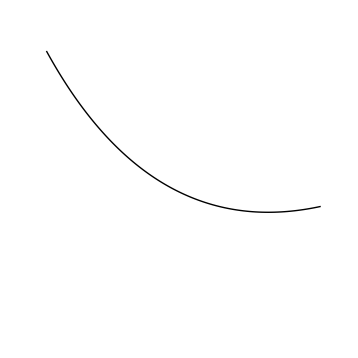

-Graphics3D-

-Graphics3D-

```mathematica
curves2d= ParallelTable[CurveRenderer2D[phenotypes⟦genom⟧, numCurves,render3dres, 2Pi/2, 50],{genom, 1,numGenoms}];
graphics = ParallelTable[Graphics[curves2d⟦genom⟧,PlotRange->{{0,imgSpace⟦1⟧},{0,imgSpace⟦2⟧}}, ImageSize->{{0,imgSpace⟦1⟧},{0,imgSpace⟦2⟧}}],{genom, 1,numGenoms}]

Graphics3D[BezierCurve[phenotypes⟦1⟧,  SplineDegree->bezierOrder-1], 
ViewPoint->{1,0,0},
 Axes -> True,
 AxesLabel->{"x","y","z"},
PlotRange->plotRange]

Graphics3D[BezierCurve[phenotypes⟦1⟧,  SplineDegree->bezierOrder-1], 
ViewPoint->RotationTransform[Pi/2,{0,0,1}][{1,0,0}], 
Axes -> True, AxesLabel->{"x","y","z"},
PlotRange->plotRange]
```

```mathematica
RotationTransform[Pi/2,{0,0,1}][{1,0,0}]
```

{0,1,0}

```mathematica
r =RotationTransform[Pi/2,{1,0,0}]
r[{0,0,1.5}]
```

TransformationFunction[(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)]

{0.,-1.5,0.}

```mathematica
RotationTransform[θ,{0,0,1}][{3,0,3}]
```

{3 Cos[θ],3 Sin[θ],3}

```mathematica
Animate[With[{v=RotationTransform[θ,{0,0,1}][{3,0,0}]},Row[{
Graphics3D[{Sphere[],Cuboid[],Red,PointSize[Large],Point[v],Line[{v,{0,0,0}}],FaceForm[],EdgeForm[Black],Cuboid[{-1,-1,-1},{1,1,1}]},PlotRange->3,BoxStyle->Gray],
Graphics3D[{Sphere[],Cuboid[]},ViewPoint->v,SphericalRegion->True]}]],{θ,0,2Pi},AnimationRunning->False]
```

```mathematica
MatrixForm[{{0,0},{1,0},{0,1}}]
```

(0 | 0
1 | 0
0 | 1)

```mathematica
MatrixForm[RotationMatrix[Pi/2,{1,0,0}]]
```

(1 | 0 | 0
0 | 0 | -1
0 | 1 | 0)

```mathematica
{{1,2,3},{1,2,3}}-50
```

{{-49,-48,-47},{-49,-48,-47}}

```mathematica
RotationMatrix[0,{1,0,0}]
```

{{1,0,0},{0,1,0},{0,0,1}}